```mathematica
directory=FileNameJoin[{$HomeDirectory,"Box Sync","Research","DataRuns","2018-10-08_SpectrumAnalyzer2nd"}]
SetDirectory[directory]
```

C:\Users\kahrendsen2\Box Sync\Research\DataRuns\2018-10-08_SpectrumAnalyzer2nd

C:\Users\kahrendsen2\Box Sync\Research\DataRuns\2018-10-08_SpectrumAnalyzer2nd

```mathematica
folderString="0000";
FileNames["*",{"ALL"<>folderString}]
```

{ALL0000\A0000CH1.CSV,ALL0000\A0000CH2.CSV,ALL0000\A0000DS.BMP,ALL0000\A0000DS.SET}

```mathematica
rawImport=Import[FileNameJoin[{"ALL"<>folderString,"A"<>folderString<>"CH1.CSV"}],"csv"]
rawImport2=Import[FileNameJoin[{"ALL"<>folderString,"A"<>folderString<>"CH2.CSV"}],"csv"]
image=Import[FileNameJoin[{"ALL"<>folderString,"A"<>folderString<>"DS.BMP"}]]
```

{{Memory Length,4000,},{Trigger Level,0.,},{Source,CH1,},{Probe,1X,},{Vertical Units,V,},{Vertical Scale,1.,},{Vertical Position,-0.56,},{Horizontal Units,s,},{Horizontal Scale,0.00025,},{Horizontal Position,0.00002,},{Horizontal Mode,Main,},{Sampling Period,1.×10^-6,},{Firmware,V1.23,},{Time,,},{Mode,Fast,},{Waveform Data,},{5,},{5,},{5,},{5,},{5,},{6,},{6,},{6,},{6,},{6,},{7,},{7,},{7,},{7,},{8,},{9,},3952,{-3,},{-3,},{-3,},{-3,},{-3,},{-3,},{-2,},{-2,},{-2,},{-2,},{-1,},{-1,},{-1,},{-1,},{0,},{0,},{0,},{1,},{0,},{1,},{1,},{1,},{2,},{2,},{2,},{3,},{3,},{3,},{3,},{3,},{4,},{3,}}
 |  |  |  |

{{Memory Length,4000,},{Trigger Level,0.,},{Source,CH2,},{Probe,1X,},{Vertical Units,V,},{Vertical Scale,0.5,},{Vertical Position,-1.,},{Horizontal Units,s,},{Horizontal Scale,0.00025,},{Horizontal Position,0.00002,},{Horizontal Mode,Main,},{Sampling Period,1.×10^-6,},{Firmware,V1.23,},{Time,,},{Mode,Fast,},{Waveform Data,},{-3,},{-3,},{-3,},{-5,},{-4,},{-4,},{-4,},{-4,},{-3,},{-4,},{-5,},{-5,},{-3,},{-5,},3956,{-5,},{-5,},{-5,},{-4,},{-5,},{-5,},{-4,},{-4,},{-4,},{-4,},{-4,},{-5,},{-4,},{-5,},{-4,},{-5,},{-4,},{-4,},{-4,},{-4,},{-3,},{-4,},{-3,},{-4,},{-3,},{-4,},{-5,},{-4,},{-4,},{-5,}}
 |  |  |  |

-Graphics-

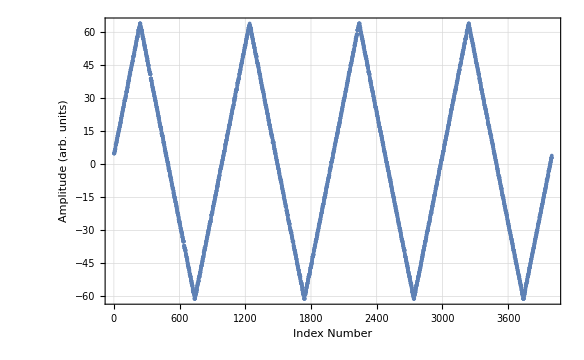

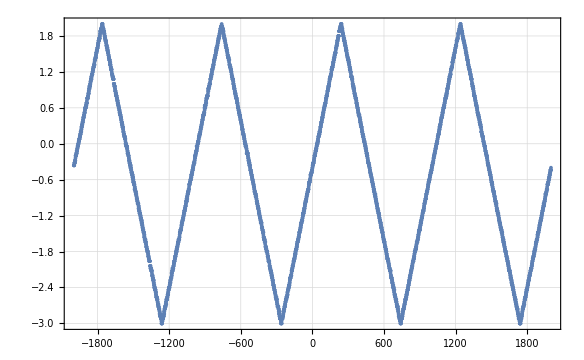

<|Memory Length→4000,Trigger Level→0.,Source→CH1,Probe→1X,Vertical Units→V,Vertical Scale→1.,Vertical Position→-0.56,Horizontal Units→s,Horizontal Scale→0.00025,Horizontal Position→0.00002,Horizontal Mode→Main,Sampling Period→1.×10^-6,Firmware→V1.23,Time→,Mode→Fast|>

```mathematica
headerEndLine=16;
pointsPerDivision=25;
headerInfo=Take[rawImport,{1,headerEndLine-1}];
headerInfo=Drop[headerInfo,None,{3}];
ha=AssociationThread[Transpose[headerInfo][[1]]->Transpose[headerInfo][[2]]]; (* ha = header associations *)
waveformData=Take[rawImport,{headerEndLine+1,-1}];
waveformData=Take[Flatten[waveformData],{1,-1,2}];
timeData=Range[-1999,2000,1]/pointsPerDivision*ha["Horizontal Scale"]*100000;
ListPlot[waveformData,FrameLabel->{"Index Number","Amplitude (arb. units)"}]
waveformDataScaled=waveformData*ha["Vertical Scale"]/pointsPerDivision;
ListPlot[Transpose[{timeData,waveformDataScaled+ha["Vertical Position"]}]]

AssociationThread[Transpose[headerInfo][[1]]->Transpose[headerInfo][[2]]]
```

```mathematica
headerEndLine=16;
pointsPerDivision=25;

ImportOscilloscopeSaveAllData[folderName_,frequencyToVoltageRatio_]:=Module[{chan1,chan2,smoothing,low,high,selectedVoltagesCh1,selectedVoltagesCh2,selectedTimes,max,maxPos,maxVoltage,voltageArray,frequencyArray,laserSpectrum,gaussModel,fit,plotTitle,yAxisTitle,xAxisTitle,model,pe,errors,data,modelPlot,plot,plotData,results},
results=<||>;
chan1=ImportOneChannelData[FileNameJoin[{folderName,StringReplace[folderName,"ALL"->"A"]<>"CH1.CSV"}]];
AppendTo[results,"Channel 1 Import"->chan1];
chan2=ImportOneChannelData[FileNameJoin[{folderName,StringReplace[folderName,"ALL"->"A"]<>"CH2.CSV"}]];
AppendTo[results,"Channel 2 Import"->chan2];
smoothing=10;

(* First, we only want the range of values on the up-sweep, so we find the min and max and only take values between those two. *)
low=Median[Position[chan1["Voltages"],Min[chan1["Voltages"]]]];
high=Median[Position[chan1["Voltages"],Max[chan1["Voltages"]]]];

(* Then we selected out just the data we want *)
selectedVoltagesCh1=Take[chan1["Voltages"],{low[[1]],high[[1]]}];
selectedVoltagesCh1=MovingAverage[selectedVoltagesCh1,smoothing];
selectedVoltagesCh2=Take[chan2["Voltages"],{low[[1]],high[[1]]}];
selectedVoltagesCh2=MovingAverage[selectedVoltagesCh2,smoothing];
selectedTimes=Take[chan1["Times"],{low[[1]],high[[1]]}];

(* Find the value of the two peaks, the space between these peaks represents the Free spectral range of the detector *)
max=Max[Take[selectedVoltagesCh2,{1,-1}]];
(* Get the index of each of these positions, so that we can obtain the voltage setting that resulted in these maximas *)
maxPos=Flatten[Position[selectedVoltagesCh2,max]][[1]];
maxVoltage=selectedVoltagesCh1[[maxPos]];

AppendTo[results,"ν2V Ratio"->frequencyToVoltageRatio];

voltageArray=QuantityArray[selectedVoltagesCh1-maxVoltage,"V"];
frequencyArray=voltageArray*frequencyToVoltageRatio;

laserSpectrum=Transpose[{QuantityMagnitude[frequencyArray],selectedVoltagesCh2}];
AppendTo[results,"Spectrum Data"->laserSpectrum];

gaussModel[x_]=A+ampl Evaluate[PDF[NormalDistribution[m,σ],x]];
fit=NonlinearModelFit[laserSpectrum,gaussModel[x],{ampl,m,σ,A},x];

plotTitle="Laser Frequency Spectrum";
xAxisTitle="Detuning (GHz)";
yAxisTitle="Intensity (arb. units)";
model=Normal[fit];
pe=fit["BestFitParameters"];(*Parameter Estimates*)
AppendTo[results,"Fit Parameters"->pe];
errors=fit["ParameterErrors"];
plotData=Transpose[{Transpose[laserSpectrum][[1]]-m/.pe,Transpose[laserSpectrum][[2]]}];
modelPlot=Plot[fit[x+m/.pe],{x,laserSpectrum[[-1]][[1]],laserSpectrum[[1]][[1]]},PlotRange->Full];
plot=Show[{ListPlot[laserSpectrum,PlotLabel-> plotTitle,FrameLabel->{xAxisTitle,yAxisTitle},PlotRange->{{-3,3},Full}],modelPlot}];
AppendTo[results,"Plot"->plot];
results
];


ImportOscilloscopeSaveAllReferenceData[folderName_]:=Module[{chan1,chan2,smoothing,low,high,selectedVoltagesCh1,selectedVoltagesCh2,selectedTimes,firstHalfMax,secondHalfMax,max1Pos,max2Pos,max1Voltage,max2Voltage,voltageDifference,freeSpectralRange,frequencyToVoltageRatio,voltageArray,frequencyArray,laserSpectrum,gaussModel,fit,plotTitle,yAxisTitle,xAxisTitle,model,pe,errors,data,modelPlot,plot,plotData,results},
results=<||>;
chan1=ImportOneChannelData[FileNameJoin[{folderName,StringReplace[folderName,"ALL"->"A"]<>"CH1.CSV"}]];
AppendTo[results,"Channel 1 Import"->chan1];
chan2=ImportOneChannelData[FileNameJoin[{folderName,StringReplace[folderName,"ALL"->"A"]<>"CH2.CSV"}]];
AppendTo[results,"Channel 2 Import"->chan2];
smoothing=10;

(* First, we only want the range of values on the up-sweep, so we find the min and max and only take values between those two. *)
low=Median[Position[chan1["Voltages"],Min[chan1["Voltages"]]]];
high=Median[Position[chan1["Voltages"],Max[chan1["Voltages"]]]];

(* Then we selected out just the data we want *)
selectedVoltagesCh1=Take[chan1["Voltages"],{low[[1]],high[[1]]}];
selectedVoltagesCh1=MovingAverage[selectedVoltagesCh1,smoothing];
selectedVoltagesCh2=Take[chan2["Voltages"],{low[[1]],high[[1]]}];
selectedVoltagesCh2=MovingAverage[selectedVoltagesCh2,smoothing];
selectedTimes=Take[chan1["Times"],{low[[1]],high[[1]]}];

(* Find the value of the two peaks, the space between these peaks represents the Free spectral range of the detector *)
firstHalfMax=Max[Take[selectedVoltagesCh2,{1,Ceiling[Length[selectedVoltagesCh2]/2]}]];
secondHalfMax=Max[Take[selectedVoltagesCh2,{Ceiling[Length[selectedVoltagesCh2]/2],-1}]];

(* Get the index of each of these positions, so that we can obtain the voltage setting that resulted in these maximas *)
max1Pos=Flatten[Position[selectedVoltagesCh2,firstHalfMax]][[1]];
max2Pos=Flatten[Position[selectedVoltagesCh2,secondHalfMax]][[1]];

max1Voltage=selectedVoltagesCh1[[max1Pos]];
max2Voltage=selectedVoltagesCh1[[max2Pos]];

(* Calculate the difference in voltage between the two peaks *)
voltageDifference=Quantity[max2Voltage-max1Voltage,"V"];
AppendTo[results,"Peak to Peak Voltage"->voltageDifference];
freeSpectralRange=Quantity[7.5,"GHz"];
frequencyToVoltageRatio=freeSpectralRange/voltageDifference;
AppendTo[results,"ν2V Ratio"->frequencyToVoltageRatio];

voltageArray=QuantityArray[selectedVoltagesCh1-max1Voltage,"V"];
frequencyArray=voltageArray*frequencyToVoltageRatio;

laserSpectrum=Transpose[{QuantityMagnitude[frequencyArray],selectedVoltagesCh2}];
AppendTo[results,"Spectrum Data"->laserSpectrum];

gaussModel[x_]=A+ampl Evaluate[PDF[NormalDistribution[m,σ],x]];
fit=NonlinearModelFit[laserSpectrum,gaussModel[x],{ampl,m,σ,A},x];

plotTitle="Laser Frequency Spectrum";
xAxisTitle="Detuning (GHz)";
yAxisTitle="Intensity (arb. units)";
model=Normal[fit];
pe=fit["BestFitParameters"];(*Parameter Estimates*)
AppendTo[results,"Fit Parameters"->pe];
errors=fit["ParameterErrors"];
plotData=Transpose[{Transpose[laserSpectrum][[1]]-m/.pe,Transpose[laserSpectrum][[2]]}];
modelPlot=Plot[fit[x+m/.pe],{x,laserSpectrum[[-1]][[1]],laserSpectrum[[1]][[1]]},PlotRange->Full];
plot=Show[{ListPlot[laserSpectrum,PlotLabel-> plotTitle,FrameLabel->{xAxisTitle,yAxisTitle},PlotRange->{{-3,3},Full}],modelPlot}];
AppendTo[results,"Plot"->plot];
results
];


ImportOneChannelData[fileName_]:=Module[{rawImport,headerInfo,ha,waveformData,timeData,plot,waveformDataScaled,return,orderedPairs},
return=<||>;
rawImport=Import[fileName,"csv","Numeric"->True];
headerInfo=Take[rawImport,{1,headerEndLine-1}];
(*headerInfo=Drop[headerInfo,None,{3}];*)(* This line may or may not be needed, depending on if the file was cleaned up by deleting "empty" cells.*)
ha=AssociationThread[Transpose[headerInfo][[1]]->Transpose[headerInfo][[2]]]; (* ha = header associations *)
AppendTo[return,"Header Info"->ha];
waveformData=Take[rawImport,{headerEndLine+1,-1}];
waveformData=Take[Flatten[waveformData],{1,-1,2}];(* This line may or may not be needed, depending on if the file was cleaned up by deleting "empty" cells.*)
(*waveformData=Take[Flatten[waveformData],{1,-1}];*)(* This line may or may not be needed, depending on if the file was cleaned up by deleting "empty" cells.*)
AppendTo[return,"Raw OScope Data"->waveformData];
AppendTo[return,"Raw OScope Plot"->ListPlot[waveformData]];
timeData=Range[-1999,2000,1]/pointsPerDivision*ha["Horizontal Scale"]*100000;
AppendTo[return,"Times"->timeData];
waveformDataScaled=waveformData*ha["Vertical Scale"]/pointsPerDivision(*+ha["Vertical Position"]*);
AppendTo[return,"Voltages"->waveformDataScaled];
orderedPairs=Transpose[{timeData,waveformDataScaled}];
AppendTo[return,"Ordered Pairs"->orderedPairs];
plot=ListPlot[orderedPairs,FrameLabel->{"Time (μs)","Voltage (V)"}];
AppendTo[return,"Plot"->plot];
return
];
```

```mathematica
directory=FileNameJoin[{$HomeDirectory,"Box Sync","Research","DataRuns","2018-06-26_SpectrumAnalyzer"}]
SetDirectory[directory]
FileNames[]
```

C:\Users\kahrendsen2\Box Sync\Research\DataRuns\2018-06-26_SpectrumAnalyzer

C:\Users\kahrendsen2\Box Sync\Research\DataRuns\2018-06-26_SpectrumAnalyzer

{A0003CH1.CSV,A0003CH2.CSV,A0003DS.BMP,A0003DS.SET,ALL0000,ALL0001,ALL0002,DS0000.BMP,DS0001.BMP,DS0002.BMP,DS0002OLD.BMP,spectrumAnalyzerAnalysis.xlsx}

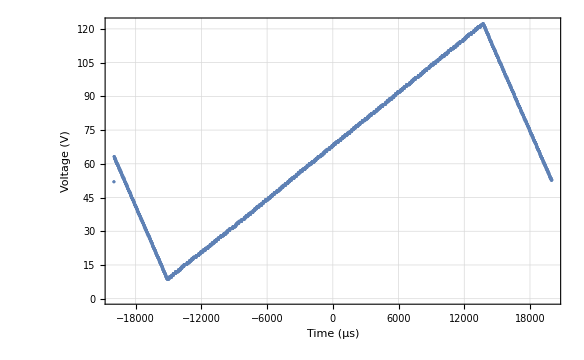
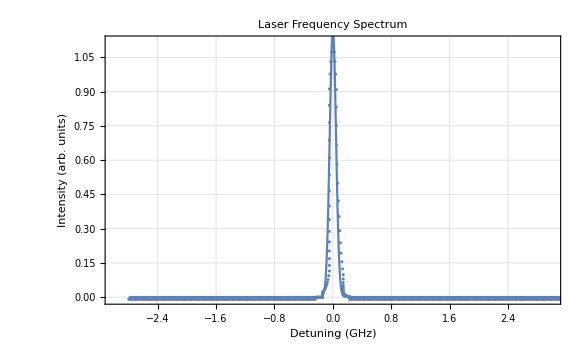
<|Channel 1 Import→<|Header Info→{{Memory Length,4000},{Trigger Level,42.},{Source,CH1},{Probe,10X},{Vertical Units,V},{Vertical Scale,20.},{Vertical Position,-70.4},{Horizontal Units,s},{Horizontal Scale,0.0025},{Horizontal Position,0.007},{Horizontal Mode,Main},{Sampling Period,0.00001},{Firmware,V1.23},{Time,},{Mode,Fast}},5,Plot→-Graphics-|>,Channel 2 Import→<|1|>,Peak to Peak Voltage→63.36 V,ν2V Ratio→0.118371 GHz/V,Spectrum Data→{{-2.79356,-0.008},{-2.79356,-0.008},2865,{10.5682,-0.008},{10.5777,-0.008}},Fit Parameters→{ampl→0.126415,m→0.0106781,σ→0.0432107,A→0.000820892},Plot→-Graphics-|>
 |  |  |  |

{Channel 1 Import,Channel 2 Import,Peak to Peak Voltage,ν2V Ratio,Spectrum Data,Fit Parameters,Plot}

{Header Info,Raw OScope Data,Raw OScope Plot,Times,Voltages,Ordered Pairs,Plot}

63.36 V

```mathematica
dat=ImportOscilloscopeSaveAllReferenceData["ALL0002"]
Keys[dat]
Keys[dat["Channel 1 Import"]]
dat["Peak to Peak Voltage"]
```

0.118371 GHz/V

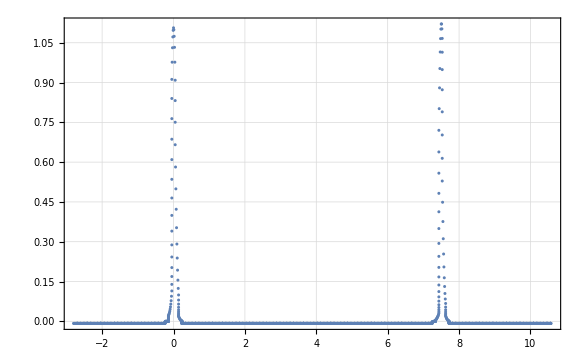

-Graphics-

{{Memory Length,4000},{Trigger Level,42.},{Source,CH2},{Probe,1X},{Vertical Units,V},{Vertical Scale,0.2},{Vertical Position,-0.608},{Horizontal Units,s},{Horizontal Scale,0.0025},{Horizontal Position,0.007},{Horizontal Mode,Main},{Sampling Period,0.00001},{Firmware,V1.23},{Time,},{Mode,Fast}}

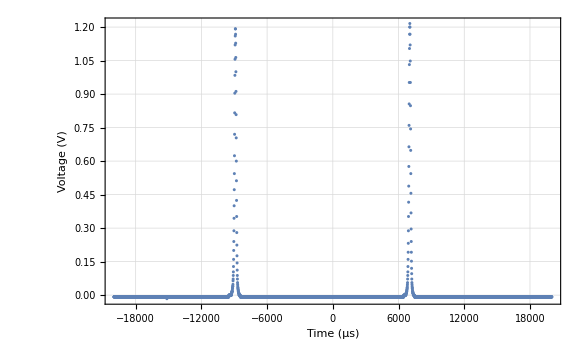

```mathematica
dat["ν2V Ratio"]
ListPlot[dat["Spectrum Data"]]
dat["Plot"]
dat["Channel 2 Import"]["Header Info"]
dat["Channel 2 Import"]["Plot"]
```